```mathematica
(*Constants*)
fm2MeV = 1/197(*Conversion from fm to MeV*);
(* all quantities are given in powers of MeV *)
μB=776;(* Barion chemical potential *)
μI3=-14.1;(* Izospin chemical potential *)
T=49.6;(* Temperature in MeV*)
H=10.0;(* Hubble like constant of fireball expansion *)
mp=938.27208816;(* Proton mass *)
mn=939.5654205;(* Neutron mass *)
md=1875.61;(* Deuteron mass *)
R=15.7 fm2MeV;(* Proton source fireball radius *)
gs=2; (* Spin degeneration of proton *)
γ =1;(* Fugacity *)
d=0.2;(*E ccentricity *)
μp=μB+1/2 μI3;(* Chemical potential of proton *)
μn=μB-1/2 μI3;(* Chemical potential of neutron *)
(************)
Rkin=R;(* Dueteron source fireball radius *)
Rd=2.12799fm2MeV; (* Deuteron radius in fm *)
```

```mathematica
(* Experimental data *)
SetDirectory[NotebookDirectory[]];
Protons = Import["protons.txt","Table"];
ProtonsY = Import["protonsY.txt","Table"];
Deuterons = Import["deuteronsmt2.txt","Table"];
DeuteronsY = Import["deuteronsY.txt","Table"];
```

```mathematica
(************************************************)
(*      flow and momentum parametrization        *)
(************************************************)
v [r_]:= Tanh[H*r];
gammaA[r_,t_]:=(1-(1+d Cos[2 t])v[r]^2)^(-1/2);
g = ({{1, 0, 0, 0}, {0, -1, 0, 0}, {0, 0, -1, 0}, {0, 0, 0, -1}});
```

```mathematica
(* spheroidal flow *)
uA[r_,t_,f_]:= gammaA[r,t]{1,v[r] √(1-d)Cos[f]Sin[t],v[r] √(1-d)Sin[t]Sin[f],v[r] √(1+d)Cos[t]};
(* four momentum of protons *)
p4p[p_,tp_,fp_]:={√(mp^2+p^2),p Cos[fp]Sin[tp],p Sin[tp]Sin[fp],p Cos[tp]};
(* four momentum of neutrons *)
p4n[p_,tp_,fp_]:={√(mn^2+p^2),p Cos[fp]Sin[tp],p Sin[tp]Sin[fp],p Cos[tp]};
(* p.u for protons and neutrons *)
pdotupA[r_,t_,f_,p_,tp_,fp_]:= FullSimplify[p4p[p,tp,fp].g.uA[r,t,f]];
pdotunA[r_,t_,f_,p_,tp_,fp_]:= FullSimplify[p4n[p,tp,fp].g.uA[r,t,f]];
```

```mathematica
(************************************************)
(*      transverse-momentum distribution         *)
(************************************************)

(* protons given by the full 3D integral *)dNpA[p_,tp_,fp_]:=gs/(2π)^2 NIntegrate[(Exp[(pdotupA[r,t,f,p,tp,fp]-μp)/T]+1)^-1 r^2 Sin[t],{f,0,2π},{t,0,π},{r,0,R}]
(* protons given by the full 3D integral - Boltzmann approximation *)
dNpAB[p_,tp_,fp_]:=gs/(2π)^2 NIntegrate[Exp[-(pdotupA[r,t,f,p,tp,fp]-μp)/T] r^2 Sin[t],{f,0,2π},{t,0,π},{r,0,R}]
(* elimination of Subscript[φ, p] *)
Ap[p_,tp_]:=gs/(2π)^2 NIntegrate[(Exp[(pdotupA[r,t,f,p,tp,0]-μp)/T]+1)^-1 r^2 Sin[t],{f,0,2π},{t,0,π},{r,0,R}]
(* analytic Boltzmann approximation *)
ApB[p_,tp_]:=gs/(2π)NIntegrate[Exp[(-gammaA[r,t](√(mp^2+p^2)-√(1+d)p v[r]Cos[t]Cos[tp])+μp)/T]BesselI[0,gammaA[r,t]/T √(1-d)p v[r]Sin[t]Sin[tp]] r^2 Sin[t],{t,0,π},{r,0,R}]
```

```mathematica
(* Timing[dNpAB[150,π/13,π/6]]
Timing[ApB[150,π/13]] *)
```

```mathematica
(* neutrons given by the full 3D integral *)dNnA[p_,tp_,fp_]:=gs/(2π)^2 NIntegrate[(Exp[(pdotunA[r,t,f,p,tp,fp]-μn)/T]+1)^-1 r^2 Sin[t],{f,0,2π},{t,0,π},{r,0,R}]
(* protons given by the full 3D integral - Boltzmann approximation *)
dNnAB[p_,tp_,fp_]:=gs/(2π)^2 NIntegrate[Exp[-(pdotunA[r,t,f,p,tp,fp]-μn)/T] r^2 Sin[t],{f,0,2π},{t,0,π},{r,0,R}]
(* elimination of Subscript[φ, p] *)
An[p_,tp_]:=gs/(2π)^2 NIntegrate[(Exp[(pdotunA[r,t,f,p,tp,0]-μn)/T]+1)^-1 r^2 Sin[t],{f,0,2π},{t,0,π},{r,0,R}]
AnB[p_,tp_]:=gs/(2π)NIntegrate[Exp[(-gammaA[r,t](√(mn^2+p^2)-√(1+d)p v[r]Cos[t]Cos[tp])+μn)/T]BesselI[0,gammaA[r,t]/T √(1-d)p v[r]Sin[t]Sin[tp]] r^2 Sin[t],{t,0,π},{r,0,R}]
```

```mathematica
(* Timing[dNnAB[50,π/13,π/6]]
Timing[AnB[50,π/13]] *)
```

```mathematica
(************************************************)
(*              rapidity distribution            *)
(************************************************)Apy[y_]:=Cosh[y]NIntegrate[Ap[√(x^2-mp^2+x^2 Sinh[y]^2),ArcCos[(x Sinh[y])/(√(x^2-mp^2+x^2 Sinh[y]^2))]] x^2,{x,mp, mp+800}]
```

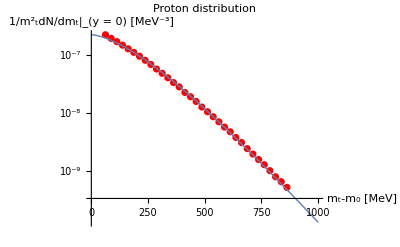

```mathematica
(************************************************)
(*  PLOT - transverse-momentum distributions     *)
(************************************************)
dP=Quiet[Show[ListLogPlot[Protons,PlotStyle->Red,AxesLabel->{"m_t-m_0 [MeV]","1/((m^2)_t)dN/dm_t|_(y = 0) [MeV^-3]",Thick},PlotLabel->"Proton distribution",AxesStyle->Thick],LogPlot[Ap[√((mp+x)^2-mp^2),π/2] 77.6/(77.6+46.5),{x,0,1000},AxesLabel->{"m_t-m_0 [MeV]","1/((m^2)_t)dN/dm_t|_(y = 0) [MeV^-3]",Thick},PlotLabel->"Proton distribution",PlotStyle->Thick,AxesStyle->Thick],
PlotRange->All]]
```

```mathematica
(************************************************)
(*       PLOT - rapidity distribution            *)
(************************************************)

(* 77.6/(77.6+46.5)Apy[0.0]
77.6/(77.6+46.5)Apy[1.0]*)
```

```mathematica
(************************************************)
(*       Deuteron formation rate           *)
(************************************************)
A[R1_,R2_]:=3/4(2π)^3 Integrate[(E^(-r^2/4(1/R1^2+1/R2^2)))/(4π  R1 R2)^3 r^2 Sin[θ],{r,0,R},{θ,0,π},{ϕ,0,2π}]
A[R,Rd]
AA=67860.2
```

8028.32

67860.2

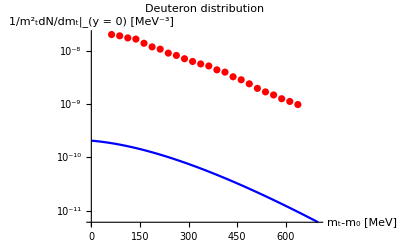

```mathematica
(************************************************)
(*      D transverse-momentum distribution       *)
(*          gaussian pair distribution           *)
(************************************************)

dD=Quiet[Show[LogPlot[A[R,Rd]/(2π) Ap[(√((md+x)^2-md^2))/2,π/2]An[(√((md+x)^2-md^2))/2,π/2],{x,0,700},PlotStyle->Blue,AxesLabel->{"m_t-m_0 [MeV]","1/((m^2)_t)dN/dm_t|_(y = 0) [MeV^-3]",Thick},PlotLabel->"Deuteron distribution",AxesStyle->Thick],ListLogPlot[Deuterons,PlotStyle->Red,AxesLabel->{"m_t-m_0 [MeV]","1/((m^2)_t)dN/dm_t|_(y = 0) [MeV^-3]"},PlotLabel->"Deuteron distribution",PlotStyle->Thick], PlotRange->All]]
```

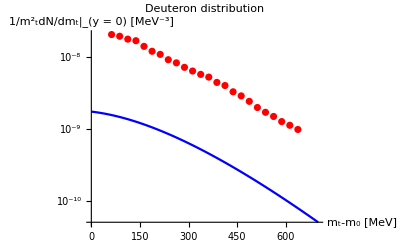

```mathematica
(************************************************)
(*      D transverse-momentum distribution       *)
(*       pair distribution in a sphere           *)
(************************************************)

dD=Quiet[Show[LogPlot[AA/(2π) Ap[(√((md+x)^2-md^2))/2,π/2]An[(√((md+x)^2-md^2))/2,π/2],{x,0,700},PlotStyle->Blue,AxesLabel->{"m_t-m_0 [MeV]","1/((m^2)_t)dN/dm_t|_(y = 0) [MeV^-3]",Thick},PlotLabel->"Deuteron distribution",AxesStyle->Thick],ListLogPlot[Deuterons,PlotStyle->Red,AxesLabel->{"m_t-m_0 [MeV]","1/((m^2)_t)dN/dm_t|_(y = 0) [MeV^-3]"},PlotLabel->"Deuteron distribution",PlotStyle->Thick], PlotRange->All]]
```

```mathematica
firstbin=AA/(2π) Ap[(√((md+x)^2-md^2))/2,π/2]An[(√((md+x)^2-md^2))/2,π/2]/.x->62.5
firstbin/(2*10^-8)
```

NIntegrate::inumr: The integrand (r^2 Sin[t])/(1+ⅇ^(0.0201613 (-768.95+Plus[«2»] Power[«2»]))) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,6.28319},{0,3.14159},{0,0.0796954}}.

NIntegrate::inumr: The integrand (r^2 Sin[t])/(1+ⅇ^(0.0201613 (-783.05+Plus[«2»] Power[«2»]))) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,6.28319},{0,3.14159},{0,0.0796954}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

1.56367×10^-9

0.0781837